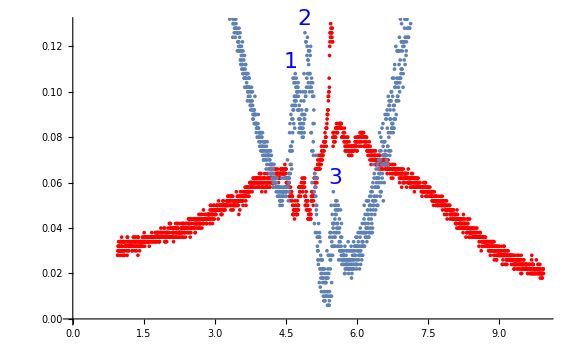

{127.823,17.4937}

{100.5,4.83144}

{114.161,11.1626}

{11.4161,1.44227}

```mathematica
SetDirectory[NotebookDirectory[]];
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
Show[ListPlot[Map[{#[[1]],#[[2]]*5-0.0388*5+0.2}&,pd],PlotStyle->Red],ListPlot[Map[{#[[1]],#[[2]]-1.17+0.2 }&,las]],Graphics[Text[Style["1",FontSize->22,FontColor->Blue],{4.6,0.113}]],Graphics[Text[Style["2",FontSize->22,FontColor->Blue],{4.9,0.132}]],Graphics[Text[Style["3",FontSize->22,FontColor->Blue],{5.55,0.062}]],Graphics[Text[Style["MOT",FontSize->18,FontColor->Red],{5.6,0.1345}]],Axes -> {True, False},ImageSize->Large]
p1 = {4.708,0.024};
p2 = {4.956, 0.024};
p3 = {5.556, 0.016};
d12 = 31.7;
d23 = 60.3;
C12 = {(p2[[1]]-p1[[1]])/d12, Sqrt[p2[[2]]^2 + p1[[2]]^2]/d12 };
C23 = {(p3[[1]]-p2[[1]])/d23, Sqrt[p3[[2]]^2 + p2[[2]]^2]/d23 };
Cinv12 = {1/C12[[1]],1/C12[[1]]^2 * C12[[2]]}
Cinv23 = {1/C23[[1]],1/C23[[1]]^2 * C23[[2]]}
CinvAvg = {Mean[{Cinv12[[1]],Cinv23[[1]]}],Mean[{Cinv12[[2]],Cinv23[[2]]}]}
mot = {0.1, 0.008};
Δ = {mot[[1]]*CinvAvg[[1]],Sqrt[mot[[1]]^2*CinvAvg[[2]]^2 + CinvAvg[[1]]^2*mot[[2]]^2]}
```

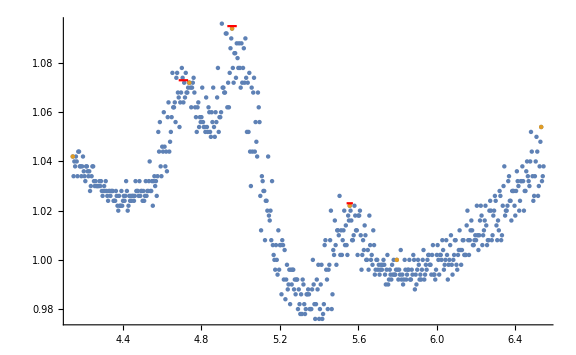

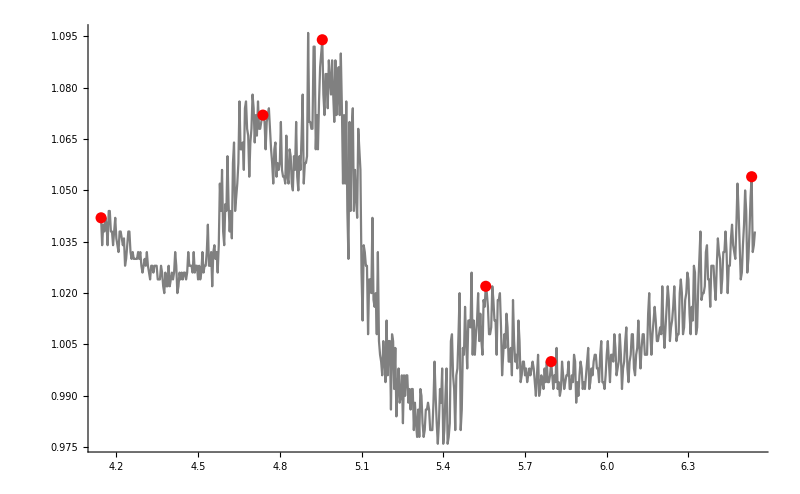

{4.738,4.956,5.556}

```mathematica
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
t = TimeSeries[las[[800;;1400]]];
Show[ListPlot[{t,FindPeaks[t,5.5]}],Plot[1.073,{x,4.708-0.024, 4.708+0.024},PlotStyle->Red],Plot[1.095,{x, 4.956-0.024,4.956+0.024},PlotStyle->Red],Plot[1.023,{x, 5.556-0.016,5.556+0.016},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[t,PlotStyle->Gray],ListPlot[FindPeaks[t,5.5],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[t,5.5]["PathTimes"][[2;;4]]
```

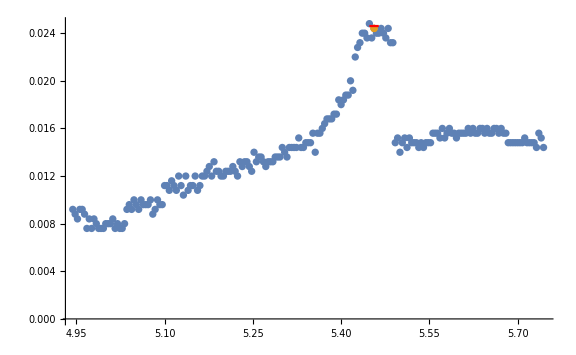

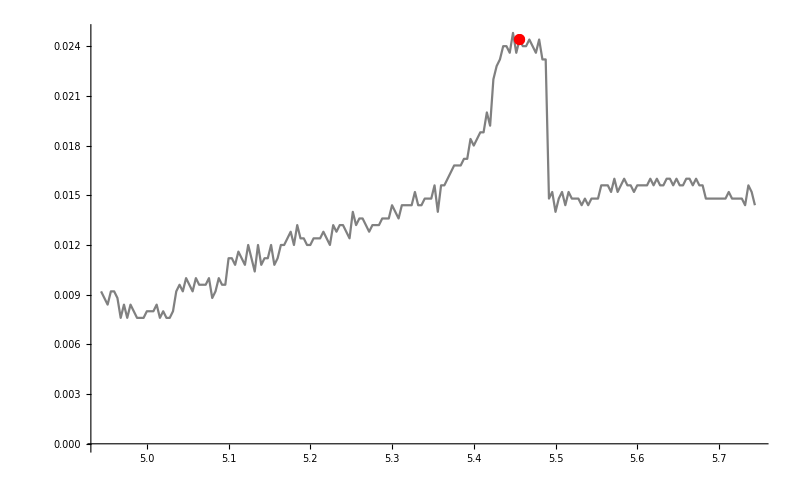

{5.456}

```mathematica
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
ts = TimeSeries[pd[[1000;;1200]]];
Show[ListPlot[{ts,FindPeaks[ts,100]}],Plot[0.0246,{x,5.456-0.008,5.456+0.008},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[ts,PlotStyle->Gray],ListPlot[FindPeaks[ts,100],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[ts,100]["PathTimes"]
```

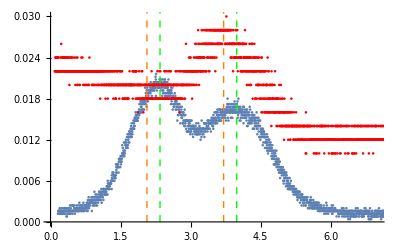

{0.298,3.706,7.166}

{2.344,3.986}

```mathematica
las2=Drop[Import["../osc/ALL0004/F0004CH1.CSV", {"Data", All, {4,5}}],-700];
pd2 = Drop[Drop[Import["../osc/ALL0004/F0004CH2.CSV",{"Data",All,{4,5}}],40],-700];
Show[ListPlot[Map[{#[[1]],#[[2]]-0.01}&,pd2]],ListPlot[Map[{#[[1]],(#[[2]]-10.75) *0.1+0.005}&,las2],PlotStyle->Red],Graphics[{Green, Dashed, Thin,Line[{{2.344,0},{2.344,0.035}}]}],
Graphics[{Green,Dashed, Thin,Line[{{3.986,0},{3.986,0.035}}]}],
Graphics[{Orange,Dashed, Thin,Line[{{3.706,0},{3.706,0.035}}]}],
Graphics[{Orange,Dashed, Thin,Line[{{2.064,0},{2.064,0.035}}]}],
PlotRange->{{0,7},{0,0.03}}]
ts2 = TimeSeries[pd2];
ts3 = TimeSeries[las2];
FindPeaks[ts3,100]["PathTimes"]
FindPeaks[ts2,100]["PathTimes"]
```

```mathematica
Γ = {2*Pi*6.0666, 2*Pi*0.0018};
Is = {1.66932, 0.00035};
PP = {10.6,0.05};
w = {0.3021, 0.0061};
Intensity[P_, ww_] := P/(Pi*ww^2/2);
II = {Intensity[PP[[1]],w[[1]]] , Sqrt[D[Intensity[P,ww],{P,1}]^2*PP[[2]]^2 + D[Intensity[P,ww],{ww,1}]^2*w[[2]]^2]}/.{ww -> w[[1]], P -> PP[[1]]}
Δν = {11.4161, 1.4423};
RR[Γ1_,Is1_,II1_,Δν1_] := Γ1/2 *(II1/Is1)/(1+II1/Is1+((2 Δν1)/Γ1)^2);
R ={( Γ/2 *(II/Is)/(1+II/Is+((2 Δν)/Γ)^2))[[1]], Sqrt[ D[RR[Γ1, Is1, II1, Δν1],{ Γ1,1}]^2 * Γ[[2]]^2 + D[RR[Γ1, Is1, II1, Δν1],{ Is1,1}]^2 * Is[[2]]^2 + 
D[RR[Γ1, Is1, II1, Δν1],{ II1,1}]^2 * II[[2]]^2 +
D[RR[Γ1, Is1, II1, Δν1],{ Δν1,1}]^2 * Δν[[2]]^2 ]}/. {Γ1 -> Γ[[1]], Is1 -> Is[[1]], II1 -> II[[1]], Δν1 -> Δν[[1]]}
diamLens = {0.025, 0.001};
distMotLens = {0.105, 0.01};
motPower = {0.168, 0.001};
PMOT[rlens_, distance_, power_] = 4 distance^2/rlens^2 *power;
totalPower = { PMOT[diamLens[[1]]/2, distMotLens[[1]],motPower[[1]]],Sqrt[D[PMOT[rlens, distance, power], {rlens, 1}]^2*(diamLens[[2]]/2)^2 + 
D[PMOT[rlens, distance, power],{distance, 1}]^2*distMotLens[[2]]^2 + D[PMOT[rlens, distance, power],{power, 1}]^2*motPower[[2]]^2],"total MOT power in μW" } /.{rlens -> diamLens[[1]]/2, distance->distMotLens[[1]], power->motPower[[1]]}
h = 6.626070040*10^(−34);
frequency = 3.8435*10^8;
MotN[power_, scatteringRate_, ν_] := power*10^(-6)/(scatteringRate*10^6*h*ν*10^6);
Population = {MotN[totalPower[[1]],R[[1]], frequency], Sqrt[D[MotN[power, scatteringRate, ν],{power,1}]^2*totalPower[[2]]^2 + D[MotN[power, scatteringRate, ν],{scatteringRate,1}]^2*R[[2]]^2]}/.{power->totalPower[[1]], scatteringRate->R[[1]],ν->frequency}
```

{73.9409,3.00633}

{18.4915,0.0433621}

{47.4163,9.8,total MOT power in μW}

{1.00687×10^7,2.08113×10^6}